```mathematica
Pattern[addition, {_,"+",_}]
```

addition:{_,+,_}

```mathematica
additionRules={__, "+",__}
```

{__,+,__}

```mathematica
MatchQ[{1, "+", 2}, additionRules]
```

True

```mathematica
commutativeGraph=[x, RelationGraph[commutativeAddition, {x,x}]][Range[100]](*Want to be able to define this functionally*)
```

```mathematica
commutativeGraph
```

commutativeGraph

```mathematica
MatchQ[1+2,2+1]
```

True

```mathematica
commutativeAddition[x_, y_]:=If[x+y==y+x, True, False]
```

```mathematica
algebra2PSet=Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\CK-12-Algebra-II-with-Trigonometry-Concepts_b_v78_eiy_s1.pdf", "Plaintext"]
```

1462420
 |  |  |  |

```mathematica
introAlgebraPSet=Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\scc_introductory_algebra_workbook_spring_2013.pdf", "Plaintext"];
```

```mathematica
calcPSet=Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\CalcI_Complete_Problems.pdf", "Plaintext"]
```

Import::general: Expected cross reference table

Import::general: Could not find document trailer

General::stop: Further output of Import::general will be suppressed during this calculation.

```mathematica
a1QsPEMDAS={ "What is 2+2", "2+3","What is 2+3", "What is 1+1", "Simplify (2-5)^2", "Simplify 2-5^2", "Simplify 10-7+1", "Simplify 10-(7+1)", "Simplify 24/(4-2)^3", "Simplify 4+5(1+12/6)^2", "Simplify (15-3)/(1+5)"}
```

{What is 2+2,2+3,What is 2+3,What is 1+1,Simplify (2-5)^2,Simplify 2-5^2,Simplify 10-7+1,Simplify 10-(7+1),Simplify 24/(4-2)^3,Simplify 4+5(1+12/6)^2,Simplify (15-3)/(1+5)}

```mathematica
a1QsFractions={"express 3 2/7 as an improper fraction", "express 12 1/3 as an improper fraction", "Express 42/5 as a mixed number", "Express 53/9 as a mixed number", "write 3/18 in simplest form", "write 42/54 in simplest form" "What is 3 2/7 as an improper fraction","What is 12 1/3 as an improper fraction","What is 42/5 as a mixed number","What is 53/9 as a mixed number","What is 3/18 in simplest form","What is 42/54 in simplest form"}
```

{express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,What is 3 2/7 as an improper fraction write 42/54 in simplest form,What is 12 1/3 as an improper fraction,What is 42/5 as a mixed number,What is 53/9 as a mixed number,What is 3/18 in simplest form,What is 42/54 in simplest form}

```mathematica
{"express 3 2/7 as an improper fraction","express 12 1/3 as an improper fraction","Express 42/5 as a mixed number","Express 53/9 as a mixed number","write 3/18 in simplest form","write 42/54 in simplest form"}
a1QsOppFrac={"Multiply 24/3 and 27/8", "Multiply 8 and 3/24", "Add 1/2 and 1/3", "What is  24/3 * 27/8", "What is  8 * 3/24", "What is  1/2 + 1/3"};
a1QsAbsoluteVal={"What is the absolute value of -1?", "What is |1|", "What is |-30|"};
a1QsNegatice={"What is 3-(-2)?", "What is -3+4"};
a1QsIntovars={"Evaluate a^2-b^2 when a=5 and b=3", "Evaluate a-b^2 when a=4 and b=2", "Evaluate a^2+b when a=7 and b=1"}
```

{express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,write 42/54 in simplest form}

{Evaluate a^2-b^2 when a=5 and b=3,Evaluate a-b^2 when a=4 and b=2,Evaluate a^2+b when a=7 and b=1}

```mathematica
{"express 3 2/7 as an improper fraction","express 12 1/3 as an improper fraction","Express 42/5 as a mixed number","Express 53/9 as a mixed number","write 3/18 in simplest form","write 42/54 in simplest form", }
```

{express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,write 42/54 in simplest form,Null}

```mathematica
a1QsCombineLikeTerms={"Combine like terms of 3a-6a+10a-a", "Combine the like terms of 5x-10y+6z-3x", "Combine like terms of 3n-5n^2+6n-10+2n^2"}
```

{Combine like terms of 3a-6a+10a-a,Combine the like terms of 5x-10y+6z-3x,Combine like terms of 3n-5n^2+6n-10+2n^2}

```mathematica
a1QsDistrbutive={"5(2x+4)", "-3(x^2-2x+7)", "-(5x^4-8)"}
```

{5(2x+4),-3(x^2-2x+7),-(5x^4-8)}

```mathematica
a1QsSolving={"8x-2=22", "-x-2=12", "2/3 x+3 =15"}
```

{8x-2=22,-x-2=12,2/3 x+3 =15}

```mathematica
a1QsPolynomials={"Factor 3x^2+4x+1", "Factor n^2+5n+6", "Factor a^2+3a+2"}
```

{Factor 3x^2+4x+1,Factor n^2+5n+6,Factor a^2+3a+2}

```mathematica
a1QsPercent={"A $750 watch is on sale for 15% off. Find the sale price.", "A salesman tells you that the $140 earrings are already marked 20% off. What
was the original price?", "Tommy’s grandma gave him a $50 gift card to Toys R Us for his birthday.
Sales tax is currently 9%. Determine the price of the most expensive toy Tommy can buy with
the $50 gift card.", "A salesman is paid a monthly salary of $2,300 plus 7% commission on his monthly sales.
Determine the amount of sales required for his total monthly income to be $3,000.", 
"What is 10% of 100", "What is 4% of 16?"}
```

{A $750 watch is on sale for 15% off. Find the sale price.,A salesman tells you that the $140 earrings are already marked 20% off. What
was the original price?,Tommy’s grandma gave him a $50 gift card to Toys R Us for his birthday.
Sales tax is currently 9%. Determine the price of the most expensive toy Tommy can buy with
the $50 gift card.,A salesman is paid a monthly salary of $2,300 plus 7% commission on his monthly sales.
Determine the amount of sales required for his total monthly income to be $3,000.,What is 10% of 100,What is 4% of 16?}

```mathematica
algebra1Questions=Flatten[{a1QsAbsoluteVal, a1QsCombineLikeTerms, a1QsDistrbutive, a1QsFractions, a1QsIntovars, a1QsPEMDAS, a1QsSolving, a1QsOppFrac, a1QsPercent, a1QsNegatice}]
```

{What is the absolute value of -1?,What is |1|,What is |-30|,Combine like terms of 3a-6a+10a-a,Combine the like terms of 5x-10y+6z-3x,Combine like terms of 3n-5n^2+6n-10+2n^2,5(2x+4),-3(x^2-2x+7),-(5x^4-8),express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,What is 3 2/7 as an improper fraction write 42/54 in simplest form,What is 12 1/3 as an improper fraction,What is 42/5 as a mixed number,What is 53/9 as a mixed number,What is 3/18 in simplest form,What is 42/54 in simplest form,Evaluate a^2-b^2 when a=5 and b=3,Evaluate a-b^2 when a=4 and b=2,Evaluate a^2+b when a=7 and b=1,What is 2+2,2+3,What is 2+3,What is 1+1,Simplify (2-5)^2,Simplify 2-5^2,Simplify 10-7+1,Simplify 10-(7+1),Simplify 24/(4-2)^3,Simplify 4+5(1+12/6)^2,Simplify (15-3)/(1+5),8x-2=22,-x-2=12,2/3 x+3 =15,Multiply 24/3 and 27/8,Multiply 8 and 3/24,Add 1/2 and 1/3,What is  24/3 * 27/8,What is  8 * 3/24,What is  1/2 + 1/3,A $750 watch is on sale for 15% off. Find the sale price.,A salesman tells you that the $140 earrings are already marked 20% off. What
was the original price?,Tommy’s grandma gave him a $50 gift card to Toys R Us for his birthday.
Sales tax is currently 9%. Determine the price of the most expensive toy Tommy can buy with
the $50 gift card.,A salesman is paid a monthly salary of $2,300 plus 7% commission on his monthly sales.
Determine the amount of sales required for his total monthly income to be $3,000.,What is 10% of 100,What is 4% of 16?,What is 3-(-2)?,What is -3+4}

```mathematica
algebra1Questionssubset={#2, Tr@Pick[#[[All]], StringMatchQ[#[[All]], #2 <>"*"]]&}
```

{#2,Tr[Pick[#1⟦All⟧,StringMatchQ[#1⟦All⟧,#2<>*]]]&}

```mathematica
a1Whatselector=StringMatchQ[#⟦All⟧, "Evaluate"]&
```

StringMatchQ[#1⟦All⟧,Evaluate]&

```mathematica
algebra1QuestionsWhat:=a1Whatselector[algebra1Questions]
```

```mathematica
algebra1QuestionsWhat
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[{What is the absolute value of -1?,What is |1|,What is |-30|,Combine like terms of 3a-6a+10a-a,Combine the like terms of 5x-10y+6z-3x,Combine like terms of 3n-5n^2+6n-10+2n^2,5(2x+4),«38»,Tommy’s grandma gave him a $50 gift card to Toys R Us for his birthday.
Sales tax is currently 9%. Determine the price of the most expensive toy Tommy can buy with
the $50 gift card.,A salesman is paid a monthly salary of $2,300 plus 7% commission on his monthly sales.
Determine the amount of sales required for his total monthly income to be $3,000.,What is 10% of 100,What is 4% of 16?,What is 3-(-2)?,«1»},Evaluate].

StringMatchQ[{What is the absolute value of -1?,What is |1|,What is |-30|,Combine like terms of 3a-6a+10a-a,Combine the like terms of 5x-10y+6z-3x,Combine like terms of 3n-5n^2+6n-10+2n^2,5(2x+4),-3(x^2-2x+7),-(5x^4-8),express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,What is 3 2/7 as an improper fraction write 42/54 in simplest form,What is 12 1/3 as an improper fraction,What is 42/5 as a mixed number,What is 53/9 as a mixed number,What is 3/18 in simplest form,What is 42/54 in simplest form,Evaluate a^2-b^2 when a=5 and b=3,Evaluate a-b^2 when a=4 and b=2,Evaluate a^2+b when a=7 and b=1,What is 2+2,2+3,What is 2+3,What is 1+1,Simplify (2-5)^2,Simplify 2-5^2,Simplify 10-7+1,Simplify 10-(7+1),Simplify 24/(4-2)^3,Simplify 4+5(1+12/6)^2,Simplify (15-3)/(1+5),8x-2=22,-x-2=12,2/3 x+3 =15,Multiply 24/3 and 27/8,Multiply 8 and 3/24,Add 1/2 and 1/3,What is  24/3 * 27/8,What is  8 * 3/24,What is  1/2 + 1/3,A $750 watch is on sale for 15% off. Find the sale price.,A salesman tells you that the $140 earrings are already marked 20% off. What
was the original price?,Tommy’s grandma gave him a $50 gift card to Toys R Us for his birthday.
Sales tax is currently 9%. Determine the price of the most expensive toy Tommy can buy with
the $50 gift card.,A salesman is paid a monthly salary of $2,300 plus 7% commission on his monthly sales.
Determine the amount of sales required for his total monthly income to be $3,000.,What is 10% of 100,What is 4% of 16?,What is 3-(-2)?,What is -3+4},Evaluate]

```mathematica
algebra2PSetList=StringSplit[algebra2PSet]
```

{CK-12,Algebra,II,with,Trigonometry,Concepts,Lori,Jordan,Kate,Dirga,SayThanks,to,theAuthors,Click,http://www.ck12.org/saythanks,(No,sign,in,required),www.ck12.org,AUTHORS,Lori,Jordan,To,access,a,customizable,version,of,this,book,,as,well,as,other,Kate,Dirga,interactive,content,,visitwww.ck12.org,CK-12,201642,cotx+tanx=2csc2x,Summary,In,this,chapter,,you,will,learn,how,to,graph,sine,,cosine,,and,tangent,as,we,well,as,what,a,trigonometric,identity,is.,You,will,use,these,identities,and,formulas,to,simplify,expressions,,prove,trigonometric,statements,,and,solve,equations.,983}
 |  |  |  |

```mathematica
algebra2PSetList=algebra2PSetList[20;;Length[algebra2PSetList]-10]
```

{CK-12,Algebra,II,with,Trigonometry,Concepts,Lori,Jordan,Kate,Dirga,SayThanks,to,theAuthors,Click,http://www.ck12.org/saythanks,(No,sign,in,required),www.ck12.org,AUTHORS,Lori,Jordan,To,access,a,customizable,version,of,this,book,,as,well,as,other,Kate,Dirga,interactive,content,,visitwww.ck12.org,CK-12,201642,cotx+tanx=2csc2x,Summary,In,this,chapter,,you,will,learn,how,to,graph,sine,,cosine,,and,tangent,as,we,well,as,what,a,trigonometric,identity,is.,You,will,use,these,identities,and,formulas,to,simplify,expressions,,prove,trigonometric,statements,,and,solve,equations.,983}[1]
 |  |  |  |

```mathematica
Position[algebra2PSetList, "ExampleA"]
```

{{0,7936},{0,8501},{0,9237},{0,10028},{0,10711},{0,11398},{0,12532},{0,13214},{0,14025},{0,14987},{0,15646},{0,16295},{0,17107},{0,17787},{0,18422},{0,19182},{0,20586},{0,21564},{0,22638},{0,23556},{0,24610},{0,25532},{0,26211},{0,26999},{0,27883},{0,29054},{0,29821},{0,30959},{0,31872},{0,33035},{0,34229},{0,34694},{0,35920},{0,36621},{0,37967},{0,38805},{0,39988},{0,40705},{0,41625},{0,42666},{0,43905},{0,44913},{0,45880},{0,47545},{0,48901},{0,50084},{0,51068},{0,51982},{0,53307},{0,54444},{0,56231},{0,57164},{0,58333},{0,59319},{0,61042},{0,61985},{0,62051},{0,63256},{0,64402},{0,65816},{0,66671},{0,67729},{0,68640},{0,69264},{0,70254},{0,70937},{0,71628},{0,72157},{0,73106},{0,74602},{0,75501},{0,75558},{0,76337},{0,77409},{0,78518},{0,79405},{0,80766},{0,81694},{0,82627},{0,83641},{0,84316},{0,85290},{0,86088},{0,86833},{0,87753},{0,88808},{0,89908},{0,91234},{0,92456},{0,93662},{0,94762},{0,95937},{0,96665},{0,97744},{0,98727},{0,99384},{0,100103},{0,100694},{0,101504},{0,102147},{0,102405},{0,103414},{0,105316},{0,106371},{0,107390},{0,109035},{0,110026},{0,110854},{0,111573},{0,112222},{0,112756},{0,112896},{0,113638},{0,114153},{0,115044},{0,116060},{0,117131},{0,118305},{0,119212},{0,120583},{0,121730},{0,122435},{0,123270},{0,124276},{0,125083},{0,126010},{0,126820},{0,127853},{0,128539},{0,129903},{0,130906},{0,131897},{0,132736},{0,133937},{0,134946},{0,136199},{0,137221},{0,138242},{0,139487},{0,140399},{0,141095},{0,142613},{0,143310},{0,143853},{0,144786},{0,145855},{0,146567},{0,147272},{0,147804},{0,149169},{0,150135},{0,151617},{0,152965},{0,154326},{0,155084},{0,156042},{0,156819},{0,157821},{0,158813},{0,160040},{0,160652},{0,161107},{0,162140},{0,163471},{0,164742},{0,166766},{0,167898},{0,169062},{0,169128},{0,170501},{0,171552},{0,172415},{0,173566},{0,174285},{0,175551},{0,176444},{0,177497},{0,178515},{0,179361},{0,180787},{0,181783},{0,182776},{0,183844},{0,185238},{0,186228},{0,187019},{0,187738},{0,189396},{0,190308},{0,191047},{0,192046},{0,193219},{0,193913},{0,194617},{0,194844},{0,195615},{0,196303},{0,196927},{0,197724},{0,198418},{0,199053},{0,199462},{0,200347},{0,200881},{0,201247}}

```mathematica
Dimensions[algebra2PSetList]
```

{1}

```mathematica
algebra2Qs=Flatten[{algebra2PSetList[[7937;;7952]], algebra2PSetList[[8502;;8510]]}]
```

Part::take: Cannot take positions 7937 through 7952 in {CK-12,Algebra,II,with,Trigonometry,Concepts,Lori,Jordan,Kate,Dirga,SayThanks,to,theAuthors,Click,http://www.ck12.org/saythanks,(No,sign,in,required),www.ck12.org,AUTHORS,Lori,Jordan,To,access,a,customizable,version,of,this,book,,as,well,as,other,Kate,Dirga,interactive,content,,visitwww.ck12.org,CK-12,Foundation,is,a,non-pro.02t,organization,with,a,mission,to,«201674»}[20;;201714].

Part::take: Cannot take positions 8502 through 8510 in {CK-12,Algebra,II,with,Trigonometry,Concepts,Lori,Jordan,Kate,Dirga,SayThanks,to,theAuthors,Click,http://www.ck12.org/saythanks,(No,sign,in,required),www.ck12.org,AUTHORS,Lori,Jordan,To,access,a,customizable,version,of,this,book,,as,well,as,other,Kate,Dirga,interactive,content,,visitwww.ck12.org,CK-12,Foundation,is,a,non-pro.02t,organization,with,a,mission,to,«201674»}[20;;201714].

1
 |  |  |  |

```mathematica
algebra2Qs
```

1
 |  |  |  |

```mathematica
algebra2PSetList[[8503;;8510]]
```

Part::take: Cannot take positions 8503 through 8510 in {CK-12,Algebra,II,with,Trigonometry,Concepts,Lori,Jordan,Kate,Dirga,SayThanks,to,theAuthors,Click,http://www.ck12.org/saythanks,(No,sign,in,required),www.ck12.org,AUTHORS,Lori,Jordan,To,access,a,customizable,version,of,this,book,,as,well,as,other,Kate,Dirga,interactive,content,,visitwww.ck12.org,CK-12,Foundation,is,a,non-pro.02t,organization,with,a,mission,to,«201674»}[20;;201714].

{CK-12,Algebra,II,with,Trigonometry,Concepts,Lori,Jordan,Kate,Dirga,SayThanks,to,theAuthors,Click,http://www.ck12.org/saythanks,(No,sign,in,required),www.ck12.org,AUTHORS,Lori,Jordan,To,access,a,customizable,version,of,this,book,,as,well,as,other,Kate,Dirga,interactive,content,,visitwww.ck12.org,201644,Summary,In,this,chapter,,you,will,learn,how,to,graph,sine,,cosine,,and,tangent,as,we,well,as,what,a,trigonometric,identity,is.,You,will,use,these,identities,and,formulas,to,simplify,expressions,,prove,trigonometric,statements,,and,solve,equations.,983}[20;;201714]⟦8503;;8510⟧
 |  |  |  |

```mathematica
algebra2Qs={"What is the most specific subset of the real numbers that -7 is a part of?", "Plot 1.25, 2/3 and 2 on a number line", "Identify the property used in the equations below as distributive, inverse or associative", "Evaluate 2x^2-9 for x=-3",  "Expand (a+b)^3", "What is (a+b)^n (Hint: What theorem is this?)", "Solve 4x-9=11", "Solve 3(x-5)+4=10", "Use the law of sines to find the missing side of this triangle", "What is the largest value for the missing side of this triangle", "What is sin(60)", "What is tan(30)", "Write 30 degrees in radians", "Write π/4 in degrees", "Is x=-8 a solution to 1/2x+6>3?",  "Solve and graph the solution to 2x-3<7", "Solve and graph the solution to |3x-1|≥10",  "How many miutes are in a day?", "Wrie the standard form of y=3/2 x+2", "Write slope intercept form for a slope of 2 and y-intercept of 12", "Find a perpedicular line of y=3x+2 with y intercept of the origin","What are the domain and range of the trigonometric functions?" , "Graph the inequality y<3x+4", "Find the equation of best fit for the below listed data", "Graph the parabola give by x^2+3x+2. Find the zeros, vertex and intercept", "What is the sum from 1 to 5 of a=10n+3", "What is the next term in the series ", "what is the sum of the geometric series from 1 to infinity of 9(1/10)^n?", "What are the discontiuities in the function y=(x+2)/(x+3x+2). Which are fundamental and which are removable?", "What is ln(1)?", "What are the domain and range of e^x and ln(x)"}
```

{What is the most specific subset of the real numbers that -7 is a part of?,Plot 1.25, 2/3 and 2 on a number line,Identify the property used in the equations below as distributive, inverse or associative,Evaluate 2x^2-9 for x=-3,Expand (a+b)^3,What is (a+b)^n (Hint: What theorem is this?),Solve 4x-9=11,Solve 3(x-5)+4=10,Use the law of sines to find the missing side of this triangle,What is the largest value for the missing side of this triangle,What is sin(60),What is tan(30),Write 30 degrees in radians,Write π/4 in degrees,Is x=-8 a solution to 1/2x+6>3?,Solve and graph the solution to 2x-3<7,Solve and graph the solution to |3x-1|≥10,How many miutes are in a day?,Wrie the standard form of y=3/2 x+2,Write slope intercept form for a slope of 2 and y-intercept of 12,Find a perpedicular line of y=3x+2 with y intercept of the origin,What are the domain and range of the trigonometric functions?,Graph the inequality y<3x+4,Find the equation of best fit for the below listed data,Graph the parabola give by x^2+3x+2. Find the zeros, vertex and intercept,What is the sum from 1 to 5 of a=10n+3,What is the next term in the series ,what is the sum of the geometric series from 1 to infinity of 9(1/10)^n?,What are the discontiuities in the function y=(x+2)/(x+3x+2). Which are fundamental and which are removable?,What is ln(1)?,What are the domain and range of e^x and ln(x)}

```mathematica
calcQspcalc={"Evaluate f(x)=3-5x-2x^2 for the below values: f(0), f(x+h), f(6-t)", "Compute  the difrence quotient for the given function",  "Find the domain of (w^3-3w+1)/(12 w-7)","Find the inverse of f (x) = 6x +15", "Find inverse of W (x) =  (9 −11x)^(1/5)", "Find the exact value of cos(5 π/6) without using a calculator", "Find the exact value of sin(-4 π/3) without using a calculator", "Solve  4sin (3t ) = 2", "Solve 4sin (3t ) = 2 in [0, 4π/3], 2cos(x/3) +2^0.5 = 0 in [−7π ,7π }", "Solve 4y sec(7 y) = −21y", "Solve 3−14sin (12t + 7) =13", "Solve 3sec(4 − 9z) − 24 = 0", "Sketch the graph of f(x)=3^(1 + 2  x)", "Sketch the graph of h(x)=8+3e^(2  t - 4)",  "Determine ln(e^4)", "Combine 2 log_4x +5 log_4y - 1/2 log_4x" , "For the function W(x)=ln(1+x^4) and the point x=1, find the secants at point Q and the tangenet line", "For the function f(x)=(8-x^2)/(x^2-4), find the values at the below listed points and th limit as x aproaches 2",  , "For the function f(y)= sin(y)/y find the value at the below listed points and the limit as y approaches 0"}
```

{Evaluate f(x)=3-5x-2x^2 for the below values: f(0), f(x+h), f(6-t),Compute  the difrence quotient for the given function,Find the domain of (w^3-3w+1)/(12 w-7),Find the inverse of f (x) = 6x +15,Find inverse of W (x) =  (9 −11x)^(1/5),Find the exact value of cos(5 π/6) without using a calculator,Find the exact value of sin(-4 π/3) without using a calculator,Solve  4sin (3t ) = 2,Solve 4sin (3t ) = 2 in [0, 4π/3], 2cos(x/3) +2^0.5 = 0 in [−7π ,7π },Solve 4y sec(7 y) = −21y,Solve 3−14sin (12t + 7) =13,Solve 3sec(4 − 9z) − 24 = 0,Sketch the graph of f(x)=3^(1 + 2  x),Sketch the graph of h(x)=8+3e^(2  t - 4),Determine ln(e^4),Combine 2 log_4x +5 log_4y - 1/2 log_4x,For the function W(x)=ln(1+x^4) and the point x=1, find the secants at point Q and the tangenet line,For the function f(x)=(8-x^2)/(x^2-4), find the values at the below listed points and th limit as x aproaches 2,Null,For the function f(y)= sin(y)/y find the value at the below listed points and the limit as y approaches 0}

```mathematica
calcQsderivs={"For the function f(x)=(8-x^2)/(x^2-4), use L'Hoptial's rule to find the limit as x aproaches 2",  "For the function (2-(t^2+3)^(1/2))/(t+1), L'Hoptial's rule to find the limit as x approaches -1", "Use the definition of the derivative to find the derivative of f(x)=6", "Use the definition of the derivative to find the derivative of V (t ) = 3−14t", 
 "Use the definition of the derivative to find the derivative of z(n)= (n+1)/(n+4)",
"Use the chain rule to find the derivative of Q(t)=(3t^3-4)^(1/2)", "Use the quotient rule to find the derivative of z(n)= (z+1)^(1/2)/(z+4)", 
"Find the deriviative of f (x) = 2cos(x) − 6sec(x) + 3", "Find the deriviative of g (z) =10 tan (z) − 2cot (z)", "Find the deriviative of  tan (w)sec(w)", "Find the deriviative of R(t)=(t+ tan(t))/(1+csc(t))", "Find the derivative of f(x)=2e^x-8^x", "Find the derivative of g(t)=4 log_3(t)-ln(t)", "Find the derivative of 2 cos(x)+arccos(x)" , "Find the derivative of x^2/y^3=1", "Find extrema of f(x)=12+6x^2-x^3", "Find extrema of g(w)=tan (w)sec(w)", "find the taylor expanision of g(w)=tan (w)sec(w) at w=π/4", "Find the MacLauren Expanision of z(n)= (z+1)^(1/2)/(z+4)", "Find the Derivative", "What is the Deriviative", "Evaluate the derivative"}
```

{For the function f(x)=(8-x^2)/(x^2-4), use L'Hoptial's rule to find the limit as x aproaches 2,For the function (2-(t^2+3)^(1/2))/(t+1), L'Hoptial's rule to find the limit as x approaches -1,Use the definition of the derivative to find the derivative of f(x)=6,Use the definition of the derivative to find the derivative of V (t ) = 3−14t,Use the definition of the derivative to find the derivative of z(n)= (n+1)/(n+4),Use the chain rule to find the derivative of Q(t)=(3t^3-4)^(1/2),Use the quotient rule to find the derivative of z(n)= (z+1)^(1/2)/(z+4),Find the deriviative of f (x) = 2cos(x) − 6sec(x) + 3,Find the deriviative of g (z) =10 tan (z) − 2cot (z),Find the deriviative of  tan (w)sec(w),Find the deriviative of R(t)=(t+ tan(t))/(1+csc(t)),Find the derivative of f(x)=2e^x-8^x,Find the derivative of g(t)=4 log_3(t)-ln(t),Find the derivative of 2 cos(x)+arccos(x),Find the derivative of x^2/y^3=1,Find extrema of f(x)=12+6x^2-x^3,Find extrema of g(w)=tan (w)sec(w),find the taylor expanision of g(w)=tan (w)sec(w) at w=π/4,Find the MacLauren Expanision of z(n)= (z+1)^(1/2)/(z+4),Find the Derivative,What is the Deriviative,Evaluate the derivative}

```mathematica
calcQsIntegral={"Find ∫6x^5 −18x^2 + 7 dx", "Find ∫6x^5 dx −18x + 7", "Evaluate ∫z^6 + 4z^4 − z^2 dz" ,"Determine f (x) given that f'(x) = 6x^8 − 20x^4 + x^2 + 9", "Find ∫ 2cos (w) − sec(w) tan (w)dw", "Find ∫12 + csc(θ ) [sin (θ ) + csc(θ )] dθ",
"What is ∫6x^5 −18x^2 + 7 dx", "Find ∫6x^5 dx −18x + 7",
"What is the integral of sin(2x)?", "Find the area under the curve of |x| from -1 to 1", "What is the area under the curve sin^2x from 0 to π/2", "Find the integral", "What is the integral of x dx", "Derivative of f(x)=x^2"}
```

{Find ∫6x^5 −18x^2 + 7 dx,Find ∫6x^5 dx −18x + 7,Evaluate ∫z^6 + 4z^4 − z^2 dz,Determine f (x) given that f'(x) = 6x^8 − 20x^4 + x^2 + 9,Find ∫ 2cos (w) − sec(w) tan (w)dw,Find ∫12 + csc(θ ) [sin (θ ) + csc(θ )] dθ,What is ∫6x^5 −18x^2 + 7 dx,Find ∫6x^5 dx −18x + 7,What is the integral of sin(2x)?,Find the area under the curve of |x| from -1 to 1,What is the area under the curve sin^2x from 0 to π/2,Find the integral,What is the integral of x dx,Derivative of f(x)=x^2}

```mathematica
calcQs=Flatten[{calcQspcalc, calcQsIntegral, calcQsderivs}]
```

{Evaluate f(x)=3-5x-2x^2 for the below values: f(0), f(x+h), f(6-t),Compute  the difrence quotient for the given function,Find the domain of (w^3-3w+1)/(12 w-7),Find the inverse of f (x) = 6x +15,Find inverse of W (x) =  (9 −11x)^(1/5),Find the exact value of cos(5 π/6) without using a calculator,Find the exact value of sin(-4 π/3) without using a calculator,Solve  4sin (3t ) = 2,Solve 4sin (3t ) = 2 in [0, 4π/3], 2cos(x/3) +2^0.5 = 0 in [−7π ,7π },Solve 4y sec(7 y) = −21y,Solve 3−14sin (12t + 7) =13,Solve 3sec(4 − 9z) − 24 = 0,Sketch the graph of f(x)=3^(1 + 2  x),Sketch the graph of h(x)=8+3e^(2  t - 4),Determine ln(e^4),Combine 2 log_4x +5 log_4y - 1/2 log_4x,For the function W(x)=ln(1+x^4) and the point x=1, find the secants at point Q and the tangenet line,For the function f(x)=(8-x^2)/(x^2-4), find the values at the below listed points and th limit as x aproaches 2,Null,For the function f(y)= sin(y)/y find the value at the below listed points and the limit as y approaches 0,Find ∫6x^5 −18x^2 + 7 dx,Find ∫6x^5 dx −18x + 7,Evaluate ∫z^6 + 4z^4 − z^2 dz,Determine f (x) given that f'(x) = 6x^8 − 20x^4 + x^2 + 9,Find ∫ 2cos (w) − sec(w) tan (w)dw,Find ∫12 + csc(θ ) [sin (θ ) + csc(θ )] dθ,What is ∫6x^5 −18x^2 + 7 dx,Find ∫6x^5 dx −18x + 7,What is the integral of sin(2x)?,Find the area under the curve of |x| from -1 to 1,What is the area under the curve sin^2x from 0 to π/2,Find the integral,What is the integral of x dx,Derivative of f(x)=x^2,For the function f(x)=(8-x^2)/(x^2-4), use L'Hoptial's rule to find the limit as x aproaches 2,For the function (2-(t^2+3)^(1/2))/(t+1), L'Hoptial's rule to find the limit as x approaches -1,Use the definition of the derivative to find the derivative of f(x)=6,Use the definition of the derivative to find the derivative of V (t ) = 3−14t,Use the definition of the derivative to find the derivative of z(n)= (n+1)/(n+4),Use the chain rule to find the derivative of Q(t)=(3t^3-4)^(1/2),Use the quotient rule to find the derivative of z(n)= (z+1)^(1/2)/(z+4),Find the deriviative of f (x) = 2cos(x) − 6sec(x) + 3,Find the deriviative of g (z) =10 tan (z) − 2cot (z),Find the deriviative of  tan (w)sec(w),Find the deriviative of R(t)=(t+ tan(t))/(1+csc(t)),Find the derivative of f(x)=2e^x-8^x,Find the derivative of g(t)=4 log_3(t)-ln(t),Find the derivative of 2 cos(x)+arccos(x),Find the derivative of x^2/y^3=1,Find extrema of f(x)=12+6x^2-x^3,Find extrema of g(w)=tan (w)sec(w),find the taylor expanision of g(w)=tan (w)sec(w) at w=π/4,Find the MacLauren Expanision of z(n)= (z+1)^(1/2)/(z+4),Find the Derivative,What is the Deriviative,Evaluate the derivative}

```mathematica
Clear[questionClassifier]
questionClassifier=Classify[<|"algebra 1"->algebra1Questions, "algebra 2"->algebra2Qs, "calc"->calcQs|>, Method->"NaiveBayes"]
```

ClassifierFunction[…]

```mathematica
equivilentFraction[x_, y_, n_]:= n*x/y ;
```

```mathematica
turnOffEquivFrac[question_]:=MatchQ[question, {__, "Fraction",__,"implest form"}]
```

```mathematica
Function[question,MatchQ[question,{"Fraction",__,"implest form"}]]
```

Function[question,MatchQ[question,{Fraction,__,implest form}]]

```mathematica
allpoints[question_]:=MatchQ[question, {__, "all points", __}]
```

```mathematica
eitherPointfirst[a_, b_,c_, d_]:= {{"(",a, b, ")"},{"("c, d")"}}-> {{"("c, d")"},{"(",a, b, ")"}}
```

```mathematica
isPoint[answer_]:=MatchQ[answer, {"("__")"}]
```

```mathematica
commutative[a_,b_]:=a+b-> b+a
```

```mathematica
distributive[a_,b_, c_]:=a*(b+c)-> a*b+a*c
```

```mathematica
commutativemulti[a_, b_]:=a*b-> b*a;
associative[a_, b_, c_]:=a+(b+c)-> (a+b)+c;
associativemulti[a_, b_,c_]:=a*(b*c)-> (a*b)*c;
```

```mathematica
isMatrix[answer_]:=MatchQ[answer, MatrixForm]
```

```mathematica
questionClassifier[Flatten[{algebra1Questions, algebra2Qs, calcQs}]] 
{"algebra 1","calc","calc","algebra 1","algebra 1","calc","calc","algebra 1","calc","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","calc","algebra 1","calc","algebra 1","algebra 1","algebra 1","algebra 1","calc","calc","algebra 1","calc","calc","calc","algebra 1","calc","algebra 1","calc","algebra 1","algebra 1","calc","calc","algebra 1","calc","calc","algebra 1","calc","algebra 1","calc","calc","algebra 1","calc","calc","algebra 1","calc","calc","calc","algebra 1","algebra 1","calc","calc","calc","algebra 1","algebra 1","calc","algebra 1","algebra 1","algebra 1","calc","calc","algebra 1","algebra 1","calc","calc","calc","algebra 1","calc","algebra 1","calc","calc","calc","calc","calc","algebra 1","calc","algebra 1","calc","calc","algebra 1","calc","calc","algebra 1","calc","calc","algebra 1","calc","calc","calc","calc","calc","calc","calc","algebra 1","calc","algebra 1","calc","calc","calc","calc","calc","algebra 1","algebra 1","algebra 1","calc","algebra 1","calc","calc","algebra 1","algebra 1","calc","algebra 1","calc","calc","calc","calc","calc","calc","algebra 1","algebra 1","calc","calc","calc","calc","calc","calc","algebra 1","calc","calc","calc","algebra 1","calc","calc","calc"}
questionClassifier["what is 1 plus 2"]
"algebra 1"

questionClassifier["What is the integral of x dx"]
"algebra 1"
questionClassifier["1+x dx"]
"algebra 1"
questionClassifier["1+1"]
"algebra 1"
(*What causes a return of algebra 2*)
questionClassifier[calcQs]
{"algebra 1","calc","calc","algebra 1","calc","calc","algebra 1","calc","calc","calc","calc","calc","calc","calc","algebra 1","calc","algebra 1","calc","calc","calc","calc","calc","algebra 1","algebra 1","algebra 1","calc","algebra 1","calc","calc","algebra 1","algebra 1","calc","algebra 1","calc","calc","calc","calc","calc","calc","algebra 1","algebra 1","calc","calc","calc","calc","calc","calc","algebra 1","calc","calc","calc","algebra 1","calc","calc","calc"}
questionClassifier[algebra1Questions]
{"algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1"}
questionClassifier["Evaluate sin(π/2)"]
"algebra 1"
(*radians returns calc*)
questionClassifier["Evaluate is sin(2x)"]
"algebra 1"
questionClassifier["What is the derivative of sin(x)"]
"algebra 1"
(*What is now bound to algebra 2, need to fix the training data*)
(*have unbound it for calc applications*)
questionClassifier[algebra2Qs]
{"algebra 1","algebra 1","calc","calc","calc","algebra 1","algebra 1","calc","algebra 1","algebra 1","algebra 1","calc","calc","algebra 1","algebra 1","calc","calc","calc","algebra 1","calc","algebra 1","calc","calc","calc","calc","calc","algebra 1","calc","algebra 1","calc","calc"}
questionClassifier[algebra1Questions]
{"algebra 1","calc","calc","algebra 1","algebra 1","calc","calc","algebra 1","calc","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","algebra 1","calc","algebra 1","calc","algebra 1","algebra 1","algebra 1","algebra 1","calc","calc","algebra 1","calc","calc","calc","algebra 1","calc","algebra 1","calc","algebra 1","algebra 1","calc","calc","algebra 1","calc","calc","algebra 1","calc","algebra 1","calc","calc","algebra 1","calc","calc","algebra 1","calc","calc","calc"}
questionClassifier["What is 1+1"]
"calc"
questionClassifier["What is 1+7"]
"algebra 1"

Classify[questionClassifier, "What is 1+1"]
```

{algebra 1,calc,calc,algebra 1,algebra 1,calc,calc,algebra 1,calc,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,calc,algebra 1,calc,algebra 1,algebra 1,algebra 1,algebra 1,calc,calc,algebra 1,calc,calc,calc,algebra 1,calc,algebra 1,calc,algebra 1,algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,calc,calc,algebra 1,algebra 1,calc,calc,calc,algebra 1,algebra 1,calc,algebra 1,algebra 1,algebra 1,calc,calc,algebra 1,algebra 1,calc,calc,calc,algebra 1,calc,algebra 1,calc,calc,calc,calc,calc,algebra 1,calc,algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,calc,calc,calc,calc,calc,calc,algebra 1,calc,algebra 1,calc,calc,calc,calc,calc,algebra 1,algebra 1,algebra 1,calc,algebra 1,calc,calc,algebra 1,algebra 1,calc,algebra 1,calc,calc,calc,calc,calc,calc,algebra 1,algebra 1,calc,calc,calc,calc,calc,calc,algebra 1,calc,calc,calc,algebra 1,calc,calc,calc}

{algebra 1,calc,calc,algebra 1,algebra 1,calc,calc,algebra 1,calc,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,calc,algebra 1,calc,algebra 1,algebra 1,algebra 1,algebra 1,calc,calc,algebra 1,calc,calc,calc,algebra 1,calc,algebra 1,calc,algebra 1,algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,calc,calc,algebra 1,algebra 1,calc,calc,calc,algebra 1,algebra 1,calc,algebra 1,algebra 1,algebra 1,calc,calc,algebra 1,algebra 1,calc,calc,calc,algebra 1,calc,algebra 1,calc,calc,calc,calc,calc,algebra 1,calc,algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,calc,calc,calc,calc,calc,calc,algebra 1,calc,algebra 1,calc,calc,calc,calc,calc,algebra 1,algebra 1,algebra 1,calc,algebra 1,calc,calc,algebra 1,algebra 1,calc,algebra 1,calc,calc,calc,calc,calc,calc,algebra 1,algebra 1,calc,calc,calc,calc,calc,calc,algebra 1,calc,calc,calc,algebra 1,calc,calc,calc}

algebra 1

algebra 1

algebra 1

«5 more identical outputs»

{algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,calc,calc,calc,calc,calc,calc,algebra 1,calc,algebra 1,calc,calc,calc,calc,calc,algebra 1,algebra 1,algebra 1,calc,algebra 1,calc,calc,algebra 1,algebra 1,calc,algebra 1,calc,calc,calc,calc,calc,calc,algebra 1,algebra 1,calc,calc,calc,calc,calc,calc,algebra 1,calc,calc,calc,algebra 1,calc,calc,calc}

{algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,calc,calc,calc,calc,calc,calc,algebra 1,calc,algebra 1,calc,calc,calc,calc,calc,algebra 1,algebra 1,algebra 1,calc,algebra 1,calc,calc,algebra 1,algebra 1,calc,algebra 1,calc,calc,calc,calc,calc,calc,algebra 1,algebra 1,calc,calc,calc,calc,calc,calc,algebra 1,calc,calc,calc,algebra 1,calc,calc,calc}

{algebra 1,calc,calc,algebra 1,algebra 1,calc,calc,algebra 1,calc,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,calc,algebra 1,calc,algebra 1,algebra 1,algebra 1,algebra 1,calc,calc,algebra 1,calc,calc,calc,algebra 1,calc,algebra 1,calc,algebra 1,algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,calc,calc}

{algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1}

algebra 1

algebra 1

algebra 1

«3 more identical outputs»

{algebra 1,algebra 1,calc,calc,calc,algebra 1,algebra 1,calc,algebra 1,algebra 1,algebra 1,calc,calc,algebra 1,algebra 1,calc,calc,calc,algebra 1,calc,algebra 1,calc,calc,calc,calc,calc,algebra 1,calc,algebra 1,calc,calc}

{algebra 1,algebra 1,calc,calc,calc,algebra 1,algebra 1,calc,algebra 1,algebra 1,algebra 1,calc,calc,algebra 1,algebra 1,calc,calc,calc,algebra 1,calc,algebra 1,calc,calc,calc,calc,calc,algebra 1,calc,algebra 1,calc,calc}

{algebra 1,calc,calc,algebra 1,algebra 1,calc,calc,algebra 1,calc,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,calc,algebra 1,calc,algebra 1,algebra 1,algebra 1,algebra 1,calc,calc,algebra 1,calc,calc,calc,algebra 1,calc,algebra 1,calc,algebra 1,algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,calc,calc}

{algebra 1,calc,calc,algebra 1,algebra 1,calc,calc,algebra 1,calc,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,algebra 1,calc,algebra 1,calc,algebra 1,algebra 1,algebra 1,algebra 1,calc,calc,algebra 1,calc,calc,calc,algebra 1,calc,algebra 1,calc,algebra 1,algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,algebra 1,calc,calc,algebra 1,calc,calc,algebra 1,calc,calc,calc}

calc

calc

algebra 1

algebra 1

Classify[ClassifierFunction[…],What is 1+1]

Classify::bdfmt: Argument … should be a rule, a list of rules, or an association.

```mathematica
Classify[<|"algebra 1"->algebra1Questions, "algebra 2"->algebra2Qs, "calc"->calcQs|>,"What is 1+1"]
```

calc

```mathematica
Classify[questionClassifier, "TopProbabilities"]
```

Classify::bdfmt: Argument … should be a rule, a list of rules, or an association.

Classify[ClassifierFunction[…],TopProbabilities]

```mathematica
Classify[questionClassifier, Method->"RandomForest"]
```

ClassifierFunction[…]

```mathematica
calctsetlist=questionClassifier[calcQs, {"Probability", "calc"}]
```

{0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.998534,0.997075,0.997075,0.997075,0.997075,0.997075,0.998534,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075,0.997075}

```mathematica
algebra1calctsetlist=questionClassifier[calcQs, {"Probability", "algebra 1"}]
```

{0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.000729324,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.000729324,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545,0.00145545}

```mathematica
algebra2calctsetlist=questionClassifier[calcQs, {"Probability", "algebra 2"}]
```

{0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.000736516,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.000736516,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981,0.00146981}

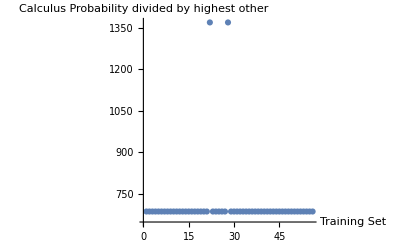

```mathematica
lp=ListPlot[#clac/#alge, AxesLabel->{"Training Set", "Calculus Probability divided by highest other"}]&@<|"clac"->calctsetlist, "alge"->algebra1calctsetlist, "alge2"-> algebra2calctsetlist|>
```

```mathematica
a2tsetlist=questionClassifier[algebra2Qs, {"Probability", "algebra 2"}]
```

{0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123,0.997123}

```mathematica
ca2tsetlist=questionClassifier[algebra2Qs, {"Probability", "calc"}]
```

{0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737,0.00143737}

```mathematica
a1a2tsetlist=questionClassifier[algebra2Qs, {"Probability", "algebra 1"}]
```

{0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934,0.00143934}

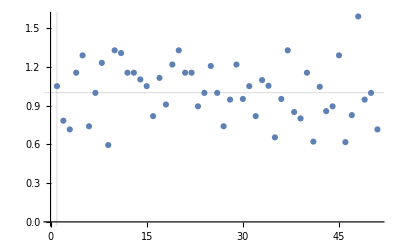

```mathematica
lp1=ListPlot[#alge1/#calc1, GridLines->{{0, 60, 1}}]&@<| "alge1"->a1tsetlist, "calc1"->ca1tsetlist|>
```

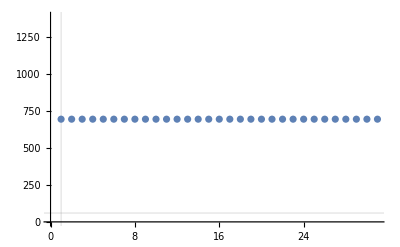

```mathematica
lp2=ListPlot[#alge2/#calc1, GridLines->{{0, 60, 1}}]&@<| "alge2"->a2tsetlist, "calc1"->ca2tsetlist, "alge1"-> a1a2tsetlist|>
```

```mathematica
Export["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\pset_trained.pdf", {lp, lp1, lp2}]
```

C:\Users\Silas Grossberndt\Documents\GitHub\WSS-Template\Final Project\Drafts\problem_sets\pset_trained.pdf

```mathematica
(*include the above graphs and the test functions to show infeasiability of doing the classifier*)
```

```mathematica
questionClassifier[calcQs]
```

{calc,calc,calc,calc,calc,calc,calc,calc,calc,calc,calc,calc,calc,calc,calc,calc,calc,calc,algebra 1,calc,algebra 1,calc,calc,calc,calc,calc,calc,calc,calc,calc,calc,calc,calc,calc,calc,algebra 1,calc,calc,calc,calc,calc,calc,calc,calc,algebra 1,algebra 1,calc,calc,calc,calc,calc,calc,calc,calc,calc}

```mathematica
questionClassifier[calcQs[[2]], {"Probabilities"}]
```

{<|algebra 1→0.323789,algebra 2→0.313684,calc→0.362526|>}

```mathematica
questionClassifier["Derivative of f(x)=x^2"]
```

calc

```mathematica
questionClassifier["Integral of 1+x dx"]
```

calc

```mathematica
questionClassifier["2+12"]
```

calc

```mathematica
questionClassifier["Derivatice of x^2"]
```

calc